## Diffusion in Two Dimensions — Steady State

## Completed and Analyzed in class, April 18, 2025

This is our twenty-first notebook. We just did one-dimensional diffusion. Now we are graduating to two-dimensional diffusion. Here is an example (this is a two-dimensional problem, not a three-dimensional one—the third dimension in the plot is just helping to visualize the temperature):

-Graphics-

This is a solution of the type of equation that we are currently studying. This is a plate that has alternating regions of hot and cold along one side, and is at an intermediate temperature along the other three sides. The full reference is here: https://youtu.be/2aJ3fFwET68.

We are going to specify the equation on the interior and the boundary conditions, and Mathematica is going to figure out the steady-state solution in the interior.

If you want to see more of the wide variety of equations that can be solved using the techniques we are using, try https://www.cfm.brown.edu/people/dobrush/am34/Mathematica/ch6/parabolic.html.

### Two-Dimensional Diffusion — Steady-State Theory

In one dimension, we had:

c(T,x) dT/dt=σ(x)(d^2 T)/(d x^2)

The obvious generalization (I won’t bore you with another derivation of combinations of second derivatives) to two dimensions is:

c(T,x,y) dT/dt=σ(x,y)((d^2 T)/(d x^2)+(d^2 T)/(d y^2))

It can be very interesting to see the time-dependent way that the system settles down to equilibrium, but now I want to make a huge simplification, which is that the system has already settled down to an equilibrium.

As long as the external sources of heat are supplied in a steady (unchanging) way, the system will eventually settle down. Once it settles down, dT/dt=0, and this is true everywhere in x and y. So for the steady state, our equations become:

0=σ(x,y)((d^2 T)/(d x^2)+(d^2 T)/(d y^2))

and T, whatever it is, is unchanging, and so it is no longer a function of t. It is only a function of x and y. We just have this as what we specify to Mathematica:

```mathematica
Module[{sigma=1},{ 0==sigma (Derivative[2,0][temp][x,y]+Derivative[0,2][temp][x,y])}] // TraditionalForm
```

{0==temp^(0,2)(x,y)+temp^(2,0)(x,y)}

### Adding the Boundary Conditions

Let’s make boundary conditions like the one pictured:

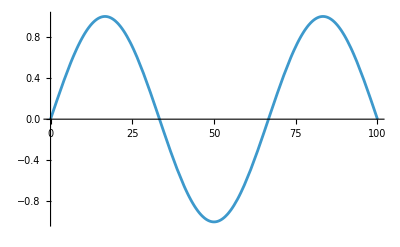

```mathematica
lengthX=100;
lengthY=60;
amplitude=1;

mode=3;
f[x_]:=amplitude Sin[mode Pi x/lengthX]
Plot[f[x],{x,0,lengthX}]
```

```mathematica
Module[{sigma=1},{ 0==sigma (Derivative[2,0][temp][x,y]+Derivative[0,2][temp][x,y]),temp[x,0]==f[x],temp[x,lengthY]==0,temp[0,y]==0,temp[lengthX,y]==0}] ;
```

### No Initial Conditions

This is a steady-state problem. Time is no longer involved. We do not need to specify any initial conditions.

```mathematica
twoDimensionalDiffusionProblem=Module[{sigma=1},{ 0==sigma (Derivative[2,0][temp][x,y]+Derivative[0,2][temp][x,y]),temp[x,0]==f[x],temp[x,lengthY]==0,temp[0,y]==0,temp[lengthX,y]==0}]
```

{0==temp^(0,2)[x,y]+temp^(2,0)[x,y],temp[x,0]==Sin[(3 π x)/100],temp[x,60]==0,temp[0,y]==0,temp[100,y]==0}

### Making Mathematica Numerically Solve the Problem

```mathematica
twoDimensionalDiffusionSolutionRule = NDSolve[twoDimensionalDiffusionProblem,temp,{x,0,lengthX},{y,0,lengthY}][[1]]
```

{temp→InterpolatingFunction[…]}

Convert the rule to a function:

```mathematica
twoDimensionalDiffusionSolution[t_,x_]=temp[x,y]/.twoDimensionalDiffusionSolutionRule
```

InterpolatingFunction[…][x,y]

### Plotting the Numerical Solution

```mathematica
Plot3D[twoDimensionalDiffusionSolution[x,y],{x,0,lengthX},{y,0,lengthY}]
```

-Graphics3D-